```mathematica
Clear["Global`*"]

Λ=1/2;
B=1;
(* To do ... figure out how to get least numerator/denominator of decimal expansion and approximate for irrationals *)
Q = 2/3;
ν=1;
μ=3/2;

polyx0 = x-b+λ q x^(q - 1);
polyx0//TraditionalForm
polyx1=polyx0/.{q->Q};
polyx1//TraditionalForm

Solve[polyx1==0,x]

polyz0=z^(2m-1)-b z^(m-1)+λ n/m;
polyz0//TraditionalForm
polyz1=polyz0/.{n->ν,m->μ};
polyz1//TraditionalForm

Solve[polyz1==0,z]
```

-b+λ q x^(q-1)+x

-b+(2 λ)/(3 x^(1/3))+x

{{x→(3 b)/4+1/12 √(9 b^2+(64 2^(1/3) λ^3)/((27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))+4 2^(2/3) (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))-1/2 √(b^2/2-(16 2^(1/3) λ^3)/(9 (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))-1/9 2^(2/3) (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3)-(3 b^3)/(2 √(9 b^2+(64 2^(1/3) λ^3)/((27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))+4 2^(2/3) (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))))},{x→(3 b)/4+1/12 √(9 b^2+(64 2^(1/3) λ^3)/((27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))+4 2^(2/3) (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))+1/2 √(b^2/2-(16 2^(1/3) λ^3)/(9 (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))-1/9 2^(2/3) (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3)-(3 b^3)/(2 √(9 b^2+(64 2^(1/3) λ^3)/((27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))+4 2^(2/3) (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))))},{x→(3 b)/4-1/12 √(9 b^2+(64 2^(1/3) λ^3)/((27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))+4 2^(2/3) (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))-1/2 √(b^2/2-(16 2^(1/3) λ^3)/(9 (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))-1/9 2^(2/3) (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3)+(3 b^3)/(2 √(9 b^2+(64 2^(1/3) λ^3)/((27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))+4 2^(2/3) (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))))},{x→(3 b)/4-1/12 √(9 b^2+(64 2^(1/3) λ^3)/((27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))+4 2^(2/3) (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))+1/2 √(b^2/2-(16 2^(1/3) λ^3)/(9 (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))-1/9 2^(2/3) (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3)+(3 b^3)/(2 √(9 b^2+(64 2^(1/3) λ^3)/((27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))+4 2^(2/3) (27 b^2 λ^3+√(729 b^4 λ^6-2048 λ^9))^(1/3))))}}

-b z^(m-1)+(λ n)/m+z^(2 m-1)

-b √z+(2 λ)/3+z^2

{{z→-1/6 √(-8 λ+(64 2^(1/3) λ^2)/((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))+((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))/2^(1/3))-1/2 √(-(16 λ)/9-(64 2^(1/3) λ^2)/(9 (729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))-((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))/(9 2^(1/3))-(6 b^2)/(√(-8 λ+(64 2^(1/3) λ^2)/((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))+((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))/2^(1/3))))},{z→-1/6 √(-8 λ+(64 2^(1/3) λ^2)/((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))+((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))/2^(1/3))+1/2 √(-(16 λ)/9-(64 2^(1/3) λ^2)/(9 (729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))-((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))/(9 2^(1/3))-(6 b^2)/(√(-8 λ+(64 2^(1/3) λ^2)/((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))+((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))/2^(1/3))))},{z→1/6 √(-8 λ+(64 2^(1/3) λ^2)/((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))+((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))/2^(1/3))-1/2 √(-(16 λ)/9-(64 2^(1/3) λ^2)/(9 (729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))-((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))/(9 2^(1/3))+(6 b^2)/(√(-8 λ+(64 2^(1/3) λ^2)/((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))+((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))/2^(1/3))))},{z→1/6 √(-8 λ+(64 2^(1/3) λ^2)/((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))+((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))/2^(1/3))+1/2 √(-(16 λ)/9-(64 2^(1/3) λ^2)/(9 (729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))-((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))/(9 2^(1/3))+(6 b^2)/(√(-8 λ+(64 2^(1/3) λ^2)/((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))+((729 b^4-1024 λ^3+27 √(729 b^8-2048 b^4 λ^3))^(1/3))/2^(1/3))))}}

```mathematica
complexGrid=Compile[{{max,_Real},{n,_Integer}},Block[{r},r=Range[-max,max,2 max/(n-1)];
Outer[Plus,-I r,r]]];

complexHSB=Compile[{{Z,_Complex,2}},Block[{h,s,b,b2},h=Arg[Z]/(2 Pi);
s=Abs[Sin[2 Pi Abs[Z]]];
b=Sqrt[Sqrt[Abs[Sin[2 Pi Im[Z]] Sin[2 Pi Re[Z]]]]];
b2=0.5 ((1-s)+b+Sqrt[(1-s-b)^2+0.01]);
Transpose[{h,Sqrt[s],b2},{3,1,2}]]];

domainImage[func_,max_,n_]:=ImageResize[ColorConvert[Image[complexHSB@func@complexGrid[max,2 n],ColorSpace->"HSB"],"RGB"],n,Resampling->"Gaussian"];

domainPlot[func_: Identity,max_: Pi,n_: 500]:=Graphics[{},Frame->True,PlotRange->max,RotateLabel->False,FrameLabel->{"Re[z]","Im[z]","Domain Colouring of "<>ToString@StandardForm@func@"z"},BaseStyle->{FontFamily->"Calibri",12},Prolog->Inset[domainImage[func,max,n],{0,0},{Center,Center},2 max]];

plotlim = 1;
ν=1;
μ=2;
l=1;
β=1;

(*
domainPlot[(#^(2μ-1)-β#^(μ-1)+l ν/μ)&,plotlim,750]

Plot3D[Abs[(x + I y)^(2μ-1)-β(x + I y)^(μ-1)+l ν/μ],{x,-plotlim,plotlim},{y,-plotlim,plotlim},AxesLabel->{"Re[z]","Im[z]"},ColorFunction->"BlueGreenYellow"]

domainPlot[(#-β+l ν/μ#^(ν/μ - 1))&,plotlim,750]
*)

myplot[ϵ_: 0.1]:=Plot[{
x,
If[x>0,Max[x ,0]+β,""],
x-β+l ν/μ x^(ν/μ - 1),
Re[(x+I ϵ) -β+l ν/μ (x + I ϵ)^(ν/μ - 1)]
},{x,-plotlim,plotlim},
PlotRange->{-2,2},
PlotLabel-> "ϵ = "<>ToString[N[Round[ϵ*100]/100]]<>", q = "<>ToString[ν]<>"/"<>ToString[μ]<>", λ = "<>ToString[l]<>", b = "<>ToString[β],
AxesLabel->Automatic,
PlotStyle->{{LightGray},{Green, Dotted},{Red,Dashed}, Black}];

axisFlip=#/.{x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;

Plot3D[Abs[(x + I y)-β+l ν/μ(x + I y)^(ν/μ - 1)],{x,-plotlim,plotlim},{y,-plotlim,plotlim},
PlotLabel-> "Absolute Value: q = "<>ToString[ν]<>"/"<>ToString[μ]<>", λ = "<>ToString[l]<>", b = "<>ToString[β],
AxesLabel->{"Re[z]","Im[z]"},
ColorFunction->ColorData["SunsetColors"]]

Plot3D[Re[(x + I y)-β+l ν/μ(x + I y)^(ν/μ - 1)],{x,-plotlim,plotlim},{y,-plotlim,plotlim},
PlotLabel-> "Real Part: q = "<>ToString[ν]<>"/"<>ToString[μ]<>", λ = "<>ToString[l]<>", b = "<>ToString[β],
AxesLabel->{"Re[z]","Im[z]"},
ColorFunction->ColorData["SunsetColors"]]//axisFlip


myplotflip[ϵ_:0.1]:= myplot[ϵ]//axisFlip;

Manipulate[
myplotflip[ϵ],
{ϵ,-1,1}]
```

-Graphics3D-

-Graphics3D-

```mathematica
N[Round[0.4444*10]/10]
```

0.4

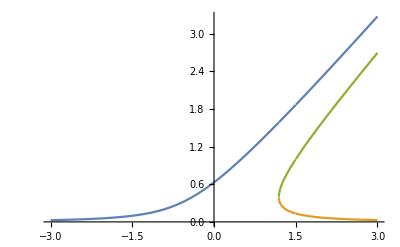

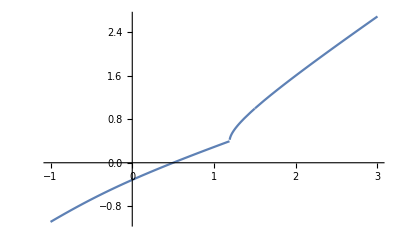

```mathematica
Clear["Global`*"]
sols=Solve[x+λ/2 x^(-1/2)==b,x];
xsols[B_]:=(x/.sols)/.{b->B};

sol1[B_,Λ_]:=xsols[b][[1]]/.{b->B,λ->Λ}
sol2[B_,Λ_]:=xsols[b][[2]]/.{b->B,λ->Λ}
sol3[B_,Λ_]:=xsols[b][[3]]/.{b->B,λ->Λ}

l=1;

Plot[{sol1[b,l],sol2[b,l],sol3[b,l]},{b,-3,3}]

(*
Manipulate[
Plot[{
Re[sol2[b+I ϵ,l]],
Re[sol3[b+I ϵ,l]],
},{b,-3,3},
PlotRange->{-2,2},
PlotLabel-> "ϵ = "<>ToString[N[Round[ϵ*100]/100]]<>", q = 1/2, λ = "<>ToString[l],
AxesLabel->Automatic],
{ϵ,0,1}]
*)

ϵ=0;
Plot[Re[sol3[b+I ϵ,l]],{b,-1,3}]

(*
Plot3D[{Re[sol2[x + I y,l]],Im[sol2[x + I y,l]]},
{x,0,2},{y,-1,1},
PlotLabel-> "Real Part: q = 1/2, λ = "<>ToString[l],
AxesLabel->{"Re[b]","Im[b]"}]
Plot3D[{Re[sol3[x + I y,l]],Im[sol3[x + I y,l]]},
{x,0,2},{y,-1,1},
PlotLabel-> "Real Part: q = 1/2, λ = "<>ToString[l],
AxesLabel->{"Re[b]","Im[b]"}]
*)
```

```mathematica
ϵ=0.1;
Re[N[sol3[1+I*ϵ,1]]]
```

0.221265